```mathematica
searchlink = "https://en.wikipedia.org/w/index.php?title=Special:Search&limit=500&offset=0&profile=default&search=computational&searchToken=b9fbzhit5sdhvvts5aa00u74l";
xmlResults = Import[searchlink, "XMLObject"];
articles = Union[Flatten[Cases[xmlResults,XMLElement[_,{_,_,
	"title"->str_String/;
		((StringMatchQ[str,StartOfString~~"Computational"~~__])&&!(StringContainsQ[str,"Journal",IgnoreCase->True])),_},_]->{str},Infinity]]];
```

```mathematica
Flatten[Table[StringTake[articles[[i]],{15;;}],{i,1,Length[articles]}]]
```

```mathematica
rawArticlesNoncomp ={"aeroacoustics","algebra","anatomy","Organization Theory","Statistical Genetics","Systems Neuroscience","Theoretical Chemistry",
"archaeology","astrophysics","auditory scene analysis","biology","Biology and Chemistry","Biology Department","chemical methods in solid-state physics",
"chemistry","Chemistry Grid","Chemistry List","cognition","complexity","Complexity Conference","complexity of mathematical operations",
"complexity theory","creativity","criminology","cybernetics","Diffie–Hellman assumption","economics","electromagnetics","engineering",
"epidemiology","epigenetics","epistemology","finance","fluid dynamics","gene","genomics","geometry","geophysics","group theory",
"hardness assumption","Heuristic Intelligence","history","human phantom","humor","immunology","indistinguishability","informatics",
"Infrastructure for Geodynamics","intelligence","irreducibility","knowledge economy","law","learning theory","lexicology","linguistics",
"lithography","logic","enhanced craft item","magnetohydrodynamics","Materials Science","mathematics","mechanics","methods for free surface flow",
"model","musicology","neurogenetic modeling","neuroscience","number theory","particle physics","photography","photography (artistic)",
"phylogenetics","physics","problem","RAM","representational understanding of mind","resource","Resource for Drug Discovery","science",
"Science & Discovery","Science Graduate Fellowship","scientist","semantics","semiotics","social choice","social science","sociology",
"statistics","Statistics & Data Analysis","steering","sustainability","theology","theory of mind","thermodynamics","thinking","topology",
"transportation science","trust","visualistics","X"};
```

```mathematica
TitleToID[article_String] := WikipediaData[article, "PageID"]
```

```mathematica
noncompPageIDs = Thread[Replace[Thread[TitleToID[rawArticlesNoncomp]], Except[_String]->0, {1}]];
```

```mathematica
IDToTitle[ID_]:=WikipediaData["PageID"-> ID,"Title"]
```

```mathematica
articlesNoncomp = Thread[Replace[Thread[IDToTitle[noncompPageIDs]],
	Except[_String]->"ARTICLE_DOES_NOT_EXIST",{1}]];
```

```mathematica
TitleToInfo[article_String]:=
	AssociationMap[WikipediaData[article, #]&,
		{"ArticlePlaintext", "ExternalLinks", "ArticleContributors", "PageID", "SummaryPlaintext", "LanguagesList", "LinksList", "BacklinksList"}];
```

```mathematica
noncompData = AssociationMap[TitleToInfo, articlesNoncomp];
```

```mathematica
DumpSave["/Users/ethan/Desktop/WSS2017/saved_data/noncompData.mx", noncompData];
DumpSave["/Users/ethan/Desktop/WSS2017/saved_data/rawArticlesNoncomp.mx", rawArticlesNoncomp];
DumpSave["/Users/ethan/Desktop/WSS2017/saved_data/articlesNoncomp.mx", articlesNoncomp];
```

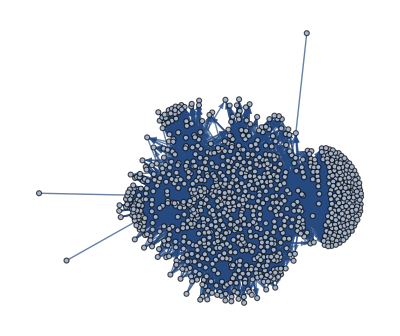

```mathematica
edgeSet = Flatten@Map[Thread, Normal@noncompData[[;;, "LinksList"]]];
theGraph = Graph[edgeSet];
verticesToKeep = Keys@Select[AssociationThread[VertexList[theGraph], VertexDegree[theGraph]], # ≥ 5 &];
filteredEdges = Select[Normal@edgeSet, And[MemberQ[verticesToKeep, #[[1]]], MemberQ[verticesToKeep, #[[2]]]] &];
Graph[filteredEdges,VertexLabels->Placed[Automatic,Tooltip]]
```